```mathematica
Clear["Global`*"]
```

I wish to detect the existence of a periodic orbit (limit cycle).  For example, the test should return FALSE (i.e. it should fail) for the left (m = 0.35) and return TRUE for the right (m = 0.3) in the following toy model.

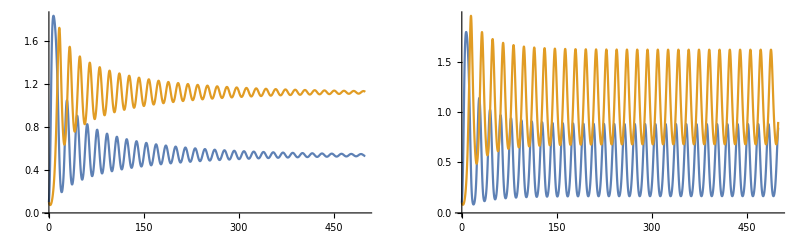

```mathematica
sys[m_]:= {
x'[t]==x[t]-0.5 x[t]^2-x[t]y[t](x[t]-1)  / (x[t]^2-1),
y'[t]==-m y[t] +  x[t]y[t](x[t]-1) / (x[t]^2-1)}

T=500;

m=0.35;
sol=First[NDSolve[{sys[m],x[0]==0.1,y[0]==0.1},{x,y},{t,0,T}]];
p=Plot[Evaluate[{x[t],y[t]}/.sol],{t,0,T}];

m=0.3;
sol2=First[NDSolve[{sys[m],x[0]==0.1,y[0]==0.1},{x,y},{t,0,T}]];
p2=Plot[Evaluate[{x[t],y[t]}/.sol2],{t,0,T}];

GraphicsRow[{p,p2}]
```

Note that I am not interested in performing local stability analysis on the system (with which the Hopf bifurcation of the above toy model could be discerned), but rather wish to assess the existence of an orbit from the numerical solution itself.

It seems that using a Poincaré section and `WhenEvent` is the way to go, but I have not figured out a way to implement it that is robust to short transients (when x’[t]==0 is true for all t>9000, an empty solution is returned) or very long transients (except by imposing a precision limit) as demonstrated by changing the period of time that is assessed.

```mathematica
test[m_]:=
Module[{res},
res=Reap[nd[{m}]=
NDSolve[{{sys[m],x[0]==0.1,y[0]==0.1},
WhenEvent[x'[t]==0&&t>Tstart,Sow[{m,Round[y[t],10^-5]}]]},
{x[t],y[t]},
{t,0,Tend},
MaxSteps->∞]][[-1,1]];
CountDistinct[res]==2
]
```

```mathematica
(* "Correct" inference *)
Tstart=4500;
Tend=5000;
test[0.35]
test[0.3]
```

False

True

```mathematica
(* False negative for m=0.3; still in transient phase *)
Tstart=450;
Tend=500;
test[0.35]
test[0.3]
```

False

False

```mathematica
(* non-existent part for m=0.35 when past transient phase *)
Tstart=45000;
Tend=50000;
test[0.35]
test[0.3]
```

Part::partw: Part 1 of {} does not exist.

False

True

I have not managed to make sense of https://mathematica.stackexchange.com/questions/96277/how-to-locate-the-position-of-a-periodic-orbit and https://mathematica.stackexchange.com/questions/164196/locating-periodic-orbits-with-mathematica.

```mathematica
test1[m_]:=
Module[{X,Y,gz,gzL,gzH,T,MinWin,MaxWin,Tol},
T=10000;
MinWin=1;
MaxWin=2000;
Tol=10^-10;
{X,Y}=NDSolveValue[{sys[m],x[0]==0.1,y[0]==0.1},{x,y},{t,0,T}];
{X,Y}=NDSolveValue[{sys[m],x[0]==X[T],y[0]==Y[T]},{x,y},{t,0,T},
AccuracyGoal->10,PrecisionGoal->10];

gz=NMinimize[{(X[T]-X[T-tp])^2+(Y[T]-Y[T-tp])^2,MinWin<tp<MaxWin},tp];
(* gz[[1]]<Tol && 1<(tp/.gz[[2]])<MaxWin-1 *)
gzL=NMinimize[{(X[T]-X[T-tp])^2+(Y[T]-Y[T-tp])^2,MinWin<tp<MaxWin},tp,Method->{"Automatic","InitialPoints"->{{MinWin+1}}}];
gzH=NMinimize[{(X[T]-X[T-tp])^2+(Y[T]-Y[T-tp])^2,MinWin<tp<MaxWin},tp,Method->{"Automatic","InitialPoints"->{{MaxWin-1}}}];
{gz,gzL,gzH}
]
```

{5.24056×10^-16,{tp→92.8143}}

{{5.24056×10^-16,{tp→92.8143}},{2.39866×10^-15,{tp→990.019}},{1.28341×10^-15,{tp→108.283}}}

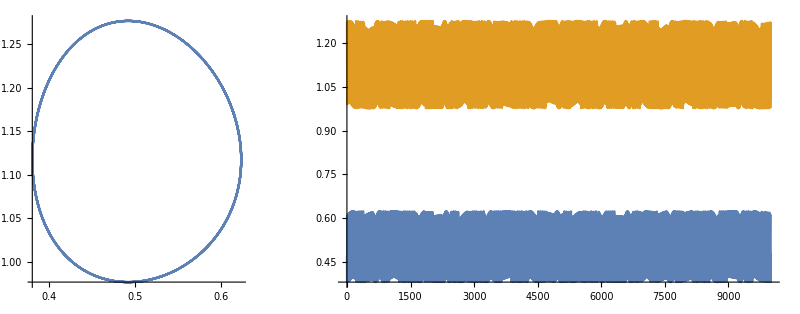

```mathematica
T=10000;
MinWin=1;
MaxWin=2000;

m=0.33;

{X,Y}=NDSolveValue[{sys[m],x[0]==0.1,y[0]==0.1},{x,y},{t,0,T}];
{X,Y}=NDSolveValue[{sys[m],x[0]==X[T],y[0]==Y[T]},{x,y},{t,0,T},
AccuracyGoal->10,PrecisionGoal->10];
gz=NMinimize[{(X[T]-X[T-tp])^2+(Y[T]-Y[T-tp])^2,MinWin<tp<MaxWin},tp]

test1[m]
GraphicsRow[{ParametricPlot[{X[t],Y[t]},{t,T-tp/. gz[[2]],T}],
Plot[Evaluate[{X[t],Y[t]}],{t,0,T}]}]
```

```mathematica
test2[m_]:=
Module[{X,Y,res,T,Tlag,Diff,Tol},
T=150000;
Tlag=100;
Tol = 10^-5;

{X,Y}=NDSolveValue[{sys[m],x[0]==0.1,y[0]==0.1},{x,y},{t,0,T},
AccuracyGoal->10,PrecisionGoal->10];

Diff=Abs[X[T]-X[T-Tlag]];
If[Diff < Tol,
res={1},
res=Reap[nd[{m}]=NDSolve[{{sys[m],x[0]==X[T],y[0]==Y[T]},
WhenEvent[x'[t]==0,Sow[{m,Round[y[t],Tol]}]]},{x[t],y[t]},{t,0,T},
AccuracyGoal->10,PrecisionGoal->10,
MaxSteps->∞]][[-1,1]]
];
CountDistinct[res]==2
]
```

```mathematica
test2[0.35]
```

False